# Analyze Adafruit GFX fonts

```mathematica
SetDirectory["../Fonts"]
```

/home/cmaier/Arduino/libraries/Adafruit_GFX_Library/Fonts

```mathematica
FileNames[]
```

{FreeMono12pt7b.h,FreeMono18pt7b.h,FreeMono24pt7b.h,FreeMono9pt7b.h,FreeMonoBold12pt7b.h,FreeMonoBold18pt7b.h,FreeMonoBold24pt7b.h,FreeMonoBold9pt7b.h,FreeMonoBoldOblique12pt7b.h,FreeMonoBoldOblique18pt7b.h,FreeMonoBoldOblique24pt7b.h,FreeMonoBoldOblique9pt7b.h,FreeMonoOblique12pt7b.h,FreeMonoOblique18pt7b.h,FreeMonoOblique24pt7b.h,FreeMonoOblique9pt7b.h,FreeSans12pt7b.h,FreeSans18pt7b.h,FreeSans24pt7b.h,FreeSans9pt7b.h,FreeSansBold12pt7b.h,FreeSansBold18pt7b.h,FreeSansBold24pt7b.h,FreeSansBold9pt7b.h,FreeSansBoldOblique12pt7b.h,FreeSansBoldOblique18pt7b.h,FreeSansBoldOblique24pt7b.h,FreeSansBoldOblique9pt7b.h,FreeSansOblique12pt7b.h,FreeSansOblique18pt7b.h,FreeSansOblique24pt7b.h,FreeSansOblique9pt7b.h,FreeSerif12pt7b.h,FreeSerif18pt7b.h,FreeSerif24pt7b.h,FreeSerif9pt7b.h,FreeSerifBold12pt7b.h,FreeSerifBold18pt7b.h,FreeSerifBold24pt7b.h,FreeSerifBold9pt7b.h,FreeSerifBoldItalic12pt7b.h,FreeSerifBoldItalic18pt7b.h,FreeSerifBoldItalic24pt7b.h,FreeSerifBoldItalic9pt7b.h,FreeSerifItalic12pt7b.h,FreeSerifItalic18pt7b.h,FreeSerifItalic24pt7b.h,FreeSerifItalic9pt7b.h,Org_01.h,Picopixel.h,Tiny3x3a2pt7b,TomThumb.h}

```mathematica
raw=Import["FreeSans9pt7b.h"]
```

const uint8_t FreeSans9pt7bBitmaps[] PROGMEM = {
  0xFF, 0xFF, 0xF8, 0xC0, 0xDE, 0xF7, 0x20, 0x09, 0x86, 0x41, 0x91, 0xFF,
  0x13, 0x04, 0xC3, 0x20, 0xC8, 0xFF, 0x89, 0x82, 0x61, 0x90, 0x10, 0x1F,
  0x14, 0xDA, 0x3D, 0x1E, 0x83, 0x40, 0x78, 0x17, 0x08, 0xF4, 0x7A, 0x35,
  0x33, 0xF0, 0x40, 0x20, 0x38, 0x10, 0xEC, 0x20, 0xC6, 0x20, 0xC6, 0x40,
  0xC6, 0x40, 0x6C, 0x80, 0x39, 0x00, 0x01, 0x3C, 0x02, 0x77, 0x02, 0x63,
  0x04, 0x63, 0x04, 0x77, 0x08, 0x3C, 0x0E, 0x06, 0x60, 0xCC, 0x19, 0x81,
  0xE0, 0x18, 0x0F, 0x03, 0x36, 0xC2, 0xD8, 0x73, 0x06, 0x31, 0xE3, 0xC4,
  0xFE, 0x13, 0x26, 0x6C, 0xCC, 0xCC, 0xC4, 0x66, 0x23, 0x10, 0x8C, 0x46,
  0x63, 0x33, 0x33, 0x32, 0x66, 0x4C, 0x80, 0x25, 0x7E, 0xA5, 0x00, 0x30,
  0xC3, 0x3F, 0x30, 0xC3, 0x0C, 0xD6, 0xF0, 0xC0, 0x08, 0x44, 0x21, 0x10,
  0x84, 0x42, 0x11, 0x08, 0x00, 0x3C, 0x66, 0x42, 0xC3, 0xC3, 0xC3, 0xC3,
  0xC3, 0xC3, 0xC3, 0x42, 0x66, 0x3C, 0x11, 0x3F, 0x33, 0x33, 0x33, 0x33,
  0x30, 0x3E, 0x31, 0xB0, 0x78, 0x30, 0x18, 0x1C, 0x1C, 0x1C, 0x18, 0x18,
  0x10, 0x08, 0x07, 0xF8, 0x3C, 0x66, 0xC3, 0xC3, 0x03, 0x06, 0x1C, 0x07,
  0x03, 0xC3, 0xC3, 0x66, 0x3C, 0x0C, 0x18, 0x71, 0x62, 0xC9, 0xA3, 0x46,
  0xFE, 0x18, 0x30, 0x60, 0xC0, 0x7F, 0x20, 0x10, 0x08, 0x08, 0x07, 0xF3,
  0x8C, 0x03, 0x01, 0x80, 0xF0, 0x6C, 0x63, 0xE0, 0x1E, 0x31, 0x98, 0x78,
  0x0C, 0x06, 0xF3, 0x8D, 0x83, 0xC1, 0xE0, 0xD0, 0x6C, 0x63, 0xE0, 0xFF,
  0x03, 0x02, 0x06, 0x04, 0x0C, 0x08, 0x18, 0x18, 0x18, 0x10, 0x30, 0x30,
  0x3E, 0x31, 0xB0, 0x78, 0x3C, 0x1B, 0x18, 0xF8, 0xC6, 0xC1, 0xE0, 0xF0,
  0x6C, 0x63, 0xE0, 0x3C, 0x66, 0xC2, 0xC3, 0xC3, 0xC3, 0x67, 0x3B, 0x03,
  0x03, 0xC2, 0x66, 0x3C, 0xC0, 0x00, 0x30, 0xC0, 0x00, 0x00, 0x64, 0xA0,
  0x00, 0x81, 0xC7, 0x8E, 0x0C, 0x07, 0x80, 0x70, 0x0E, 0x01, 0x80, 0xFF,
  0x80, 0x00, 0x1F, 0xF0, 0x00, 0x70, 0x0E, 0x01, 0xC0, 0x18, 0x38, 0x71,
  0xC0, 0x80, 0x00, 0x3E, 0x31, 0xB0, 0x78, 0x30, 0x18, 0x18, 0x38, 0x18,
  0x18, 0x0C, 0x00, 0x00, 0x01, 0x80, 0x03, 0xF0, 0x06, 0x0E, 0x06, 0x01,
  0x86, 0x00, 0x66, 0x1D, 0xBB, 0x31, 0xCF, 0x18, 0xC7, 0x98, 0x63, 0xCC,
  0x31, 0xE6, 0x11, 0xB3, 0x99, 0xCC, 0xF7, 0x86, 0x00, 0x01, 0x80, 0x00,
  0x70, 0x40, 0x0F, 0xE0, 0x06, 0x00, 0xF0, 0x0F, 0x00, 0x90, 0x19, 0x81,
  0x98, 0x10, 0x83, 0x0C, 0x3F, 0xC2, 0x04, 0x60, 0x66, 0x06, 0xC0, 0x30,
  0xFF, 0x18, 0x33, 0x03, 0x60, 0x6C, 0x0D, 0x83, 0x3F, 0xC6, 0x06, 0xC0,
  0x78, 0x0F, 0x01, 0xE0, 0x6F, 0xF8, 0x1F, 0x86, 0x19, 0x81, 0xA0, 0x3C,
  0x01, 0x80, 0x30, 0x06, 0x00, 0xC0, 0x68, 0x0D, 0x83, 0x18, 0x61, 0xF0,
  0xFF, 0x18, 0x33, 0x03, 0x60, 0x3C, 0x07, 0x80, 0xF0, 0x1E, 0x03, 0xC0,
  0x78, 0x0F, 0x03, 0x60, 0xCF, 0xF0, 0xFF, 0xE0, 0x30, 0x18, 0x0C, 0x06,
  0x03, 0xFD, 0x80, 0xC0, 0x60, 0x30, 0x18, 0x0F, 0xF8, 0xFF, 0xC0, 0xC0,
  0xC0, 0xC0, 0xC0, 0xFE, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0x0F, 0x83,
  0x0E, 0x60, 0x66, 0x03, 0xC0, 0x0C, 0x00, 0xC1, 0xFC, 0x03, 0xC0, 0x36,
  0x03, 0x60, 0x73, 0x0F, 0x0F, 0x10, 0xC0, 0x78, 0x0F, 0x01, 0xE0, 0x3C,
  0x07, 0x80, 0xFF, 0xFE, 0x03, 0xC0, 0x78, 0x0F, 0x01, 0xE0, 0x3C, 0x06,
  0xFF, 0xFF, 0xFF, 0xC0, 0x06, 0x0C, 0x18, 0x30, 0x60, 0xC1, 0x83, 0x07,
  0x8F, 0x1E, 0x27, 0x80, 0xC0, 0xD8, 0x33, 0x0C, 0x63, 0x0C, 0xC1, 0xB8,
  0x3F, 0x07, 0x30, 0xC3, 0x18, 0x63, 0x06, 0x60, 0x6C, 0x0C, 0xC0, 0xC0,
  0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xC0, 0xFF, 0xE0,
  0x3F, 0x01, 0xFC, 0x1F, 0xE0, 0xFD, 0x05, 0xEC, 0x6F, 0x63, 0x79, 0x13,
  0xCD, 0x9E, 0x6C, 0xF1, 0x47, 0x8E, 0x3C, 0x71, 0x80, 0xE0, 0x7C, 0x0F,
  0xC1, 0xE8, 0x3D, 0x87, 0x98, 0xF1, 0x1E, 0x33, 0xC3, 0x78, 0x6F, 0x07,
  0xE0, 0x7C, 0x0E, 0x0F, 0x81, 0x83, 0x18, 0x0C, 0xC0, 0x6C, 0x01, 0xE0,
  0x0F, 0x00, 0x78, 0x03, 0xC0, 0x1B, 0x01, 0x98, 0x0C, 0x60, 0xC0, 0xF8,
  0x00, 0xFF, 0x30, 0x6C, 0x0F, 0x03, 0xC0, 0xF0, 0x6F, 0xF3, 0x00, 0xC0,
  0x30, 0x0C, 0x03, 0x00, 0xC0, 0x00, 0x0F, 0x81, 0x83, 0x18, 0x0C, 0xC0,
  0x6C, 0x01, 0xE0, 0x0F, 0x00, 0x78, 0x03, 0xC0, 0x1B, 0x01, 0x98, 0x6C,
  0x60, 0xC0, 0xFB, 0x00, 0x08, 0xFF, 0x8C, 0x0E, 0xC0, 0x6C, 0x06, 0xC0,
  0x6C, 0x0C, 0xFF, 0x8C, 0x0E, 0xC0, 0x6C, 0x06, 0xC0, 0x6C, 0x06, 0xC0,
  0x70, 0x3F, 0x18, 0x6C, 0x0F, 0x03, 0xC0, 0x1E, 0x01, 0xF0, 0x0E, 0x00,
  0xF0, 0x3C, 0x0D, 0x86, 0x3F, 0x00, 0xFF, 0x86, 0x03, 0x01, 0x80, 0xC0,
  0x60, 0x30, 0x18, 0x0C, 0x06, 0x03, 0x01, 0x80, 0xC0, 0xC0, 0x78, 0x0F,
  0x01, 0xE0, 0x3C, 0x07, 0x80, 0xF0, 0x1E, 0x03, 0xC0, 0x78, 0x0F, 0x01,
  0xB0, 0x61, 0xF0, 0xC0, 0x6C, 0x0D, 0x81, 0x10, 0x63, 0x0C, 0x61, 0x04,
  0x60, 0xCC, 0x19, 0x01, 0x60, 0x3C, 0x07, 0x00, 0x60, 0xC1, 0x81, 0x30,
  0xE1, 0x98, 0x70, 0xCC, 0x28, 0x66, 0x26, 0x21, 0x13, 0x30, 0xC8, 0x98,
  0x6C, 0x4C, 0x14, 0x34, 0x0A, 0x1A, 0x07, 0x07, 0x03, 0x03, 0x80, 0x81,
  0x80, 0x60, 0x63, 0x0C, 0x30, 0xC1, 0x98, 0x0F, 0x00, 0xE0, 0x06, 0x00,
  0xF0, 0x19, 0x01, 0x98, 0x30, 0xC6, 0x0E, 0x60, 0x60, 0xC0, 0x36, 0x06,
  0x30, 0xC3, 0x0C, 0x19, 0x81, 0xD8, 0x0F, 0x00, 0x60, 0x06, 0x00, 0x60,
  0x06, 0x00, 0x60, 0x06, 0x00, 0xFF, 0xC0, 0x60, 0x30, 0x0C, 0x06, 0x03,
  0x01, 0xC0, 0x60, 0x30, 0x18, 0x06, 0x03, 0x00, 0xFF, 0xC0, 0xFB, 0x6D,
  0xB6, 0xDB, 0x6D, 0xB6, 0xE0, 0x84, 0x10, 0x84, 0x10, 0x84, 0x10, 0x84,
  0x10, 0x80, 0xED, 0xB6, 0xDB, 0x6D, 0xB6, 0xDB, 0xE0, 0x30, 0x60, 0xA2,
  0x44, 0xD8, 0xA1, 0x80, 0xFF, 0xC0, 0xC6, 0x30, 0x7E, 0x71, 0xB0, 0xC0,
  0x60, 0xF3, 0xDB, 0x0D, 0x86, 0xC7, 0x3D, 0xC0, 0xC0, 0x60, 0x30, 0x1B,
  0xCE, 0x36, 0x0F, 0x07, 0x83, 0xC1, 0xE0, 0xF0, 0x7C, 0x6D, 0xE0, 0x3C,
  0x66, 0xC3, 0xC0, 0xC0, 0xC0, 0xC0, 0xC3, 0x66, 0x3C, 0x03, 0x03, 0x03,
  0x3B, 0x67, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0x67, 0x3B, 0x3C, 0x66,
  0xC3, 0xC3, 0xFF, 0xC0, 0xC0, 0xC3, 0x66, 0x3C, 0x36, 0x6F, 0x66, 0x66,
  0x66, 0x66, 0x60, 0x3B, 0x67, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0x67,
  0x3B, 0x03, 0x03, 0xC6, 0x7C, 0xC0, 0xC0, 0xC0, 0xDE, 0xE3, 0xC3, 0xC3,
  0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0xFF, 0xFF, 0xC0, 0x30, 0x03,
  0x33, 0x33, 0x33, 0x33, 0x33, 0x33, 0xE0, 0xC0, 0x60, 0x30, 0x18, 0x4C,
  0x46, 0x63, 0x61, 0xF0, 0xEC, 0x62, 0x31, 0x98, 0x6C, 0x30, 0xFF, 0xFF,
  0xFF, 0xC0, 0xDE, 0xF7, 0x1C, 0xF0, 0xC7, 0x86, 0x3C, 0x31, 0xE1, 0x8F,
  0x0C, 0x78, 0x63, 0xC3, 0x1E, 0x18, 0xC0, 0xDE, 0xE3, 0xC3, 0xC3, 0xC3,
  0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0x3C, 0x66, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3,
  0xC3, 0x66, 0x3C, 0xDE, 0x71, 0xB0, 0x78, 0x3C, 0x1E, 0x0F, 0x07, 0x83,
  0xE3, 0x6F, 0x30, 0x18, 0x0C, 0x00, 0x3B, 0x67, 0xC3, 0xC3, 0xC3, 0xC3,
  0xC3, 0xC3, 0x67, 0x3B, 0x03, 0x03, 0x03, 0xDF, 0x31, 0x8C, 0x63, 0x18,
  0xC6, 0x00, 0x3E, 0xE3, 0xC0, 0xC0, 0xE0, 0x3C, 0x07, 0xC3, 0xE3, 0x7E,
  0x66, 0xF6, 0x66, 0x66, 0x66, 0x67, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3, 0xC3,
  0xC3, 0xC3, 0xC7, 0x7B, 0xC1, 0xA0, 0x98, 0xCC, 0x42, 0x21, 0xB0, 0xD0,
  0x28, 0x1C, 0x0C, 0x00, 0xC6, 0x1E, 0x38, 0x91, 0xC4, 0xCA, 0x66, 0xD3,
  0x16, 0xD0, 0xA6, 0x87, 0x1C, 0x38, 0xC0, 0xC6, 0x00, 0x43, 0x62, 0x36,
  0x1C, 0x18, 0x1C, 0x3C, 0x26, 0x62, 0x43, 0xC1, 0x21, 0x98, 0xCC, 0x42,
  0x61, 0xB0, 0xD0, 0x38, 0x1C, 0x0C, 0x06, 0x03, 0x01, 0x03, 0x00, 0xFE,
  0x0C, 0x30, 0xC1, 0x86, 0x18, 0x20, 0xC1, 0xFC, 0x36, 0x66, 0x66, 0x6E,
  0xCE, 0x66, 0x66, 0x66, 0x30, 0xFF, 0xFF, 0xFF, 0xFF, 0xC0, 0xC6, 0x66,
  0x66, 0x67, 0x37, 0x66, 0x66, 0x66, 0xC0, 0x61, 0x24, 0x38 };

const GFXglyph FreeSans9pt7bGlyphs[] PROGMEM = {
  {     0,   0,   0,   5,    0,    1 },   // 0x20 ' '
  {     0,   2,  13,   6,    2,  -12 },   // 0x21 '!'
  {     4,   5,   4,   6,    1,  -12 },   // 0x22 '"'
  {     7,  10,  12,  10,    0,  -11 },   // 0x23 '#'
  {    22,   9,  16,  10,    1,  -13 },   // 0x24 '$'
  {    40,  16,  13,  16,    1,  -12 },   // 0x25 '%'
  {    66,  11,  13,  12,    1,  -12 },   // 0x26 '&'
  {    84,   2,   4,   4,    1,  -12 },   // 0x27 '''
  {    85,   4,  17,   6,    1,  -12 },   // 0x28 '('
  {    94,   4,  17,   6,    1,  -12 },   // 0x29 ')'
  {   103,   5,   5,   7,    1,  -12 },   // 0x2A '*'
  {   107,   6,   8,  11,    3,   -7 },   // 0x2B '+'
  {   113,   2,   4,   5,    2,    0 },   // 0x2C ','
  {   114,   4,   1,   6,    1,   -4 },   // 0x2D '-'
  {   115,   2,   1,   5,    1,    0 },   // 0x2E '.'
  {   116,   5,  13,   5,    0,  -12 },   // 0x2F '/'
  {   125,   8,  13,  10,    1,  -12 },   // 0x30 '0'
  {   138,   4,  13,  10,    3,  -12 },   // 0x31 '1'
  {   145,   9,  13,  10,    1,  -12 },   // 0x32 '2'
  {   160,   8,  13,  10,    1,  -12 },   // 0x33 '3'
  {   173,   7,  13,  10,    2,  -12 },   // 0x34 '4'
  {   185,   9,  13,  10,    1,  -12 },   // 0x35 '5'
  {   200,   9,  13,  10,    1,  -12 },   // 0x36 '6'
  {   215,   8,  13,  10,    0,  -12 },   // 0x37 '7'
  {   228,   9,  13,  10,    1,  -12 },   // 0x38 '8'
  {   243,   8,  13,  10,    1,  -12 },   // 0x39 '9'
  {   256,   2,  10,   5,    1,   -9 },   // 0x3A ':'
  {   259,   3,  12,   5,    1,   -8 },   // 0x3B ';'
  {   264,   9,   9,  11,    1,   -8 },   // 0x3C '<'
  {   275,   9,   4,  11,    1,   -5 },   // 0x3D '='
  {   280,   9,   9,  11,    1,   -8 },   // 0x3E '>'
  {   291,   9,  13,  10,    1,  -12 },   // 0x3F '?'
  {   306,  17,  16,  18,    1,  -12 },   // 0x40 '@'
  {   340,  12,  13,  12,    0,  -12 },   // 0x41 'A'
  {   360,  11,  13,  12,    1,  -12 },   // 0x42 'B'
  {   378,  11,  13,  13,    1,  -12 },   // 0x43 'C'
  {   396,  11,  13,  13,    1,  -12 },   // 0x44 'D'
  {   414,   9,  13,  11,    1,  -12 },   // 0x45 'E'
  {   429,   8,  13,  11,    1,  -12 },   // 0x46 'F'
  {   442,  12,  13,  14,    1,  -12 },   // 0x47 'G'
  {   462,  11,  13,  13,    1,  -12 },   // 0x48 'H'
  {   480,   2,  13,   5,    2,  -12 },   // 0x49 'I'
  {   484,   7,  13,  10,    1,  -12 },   // 0x4A 'J'
  {   496,  11,  13,  12,    1,  -12 },   // 0x4B 'K'
  {   514,   8,  13,  10,    1,  -12 },   // 0x4C 'L'
  {   527,  13,  13,  15,    1,  -12 },   // 0x4D 'M'
  {   549,  11,  13,  13,    1,  -12 },   // 0x4E 'N'
  {   567,  13,  13,  14,    1,  -12 },   // 0x4F 'O'
  {   589,  10,  13,  12,    1,  -12 },   // 0x50 'P'
  {   606,  13,  14,  14,    1,  -12 },   // 0x51 'Q'
  {   629,  12,  13,  13,    1,  -12 },   // 0x52 'R'
  {   649,  10,  13,  12,    1,  -12 },   // 0x53 'S'
  {   666,   9,  13,  11,    1,  -12 },   // 0x54 'T'
  {   681,  11,  13,  13,    1,  -12 },   // 0x55 'U'
  {   699,  11,  13,  12,    0,  -12 },   // 0x56 'V'
  {   717,  17,  13,  17,    0,  -12 },   // 0x57 'W'
  {   745,  12,  13,  12,    0,  -12 },   // 0x58 'X'
  {   765,  12,  13,  12,    0,  -12 },   // 0x59 'Y'
  {   785,  10,  13,  11,    1,  -12 },   // 0x5A 'Z'
  {   802,   3,  17,   5,    1,  -12 },   // 0x5B '['
  {   809,   5,  13,   5,    0,  -12 },   // 0x5C '\'
  {   818,   3,  17,   5,    0,  -12 },   // 0x5D ']'
  {   825,   7,   7,   8,    1,  -12 },   // 0x5E '^'
  {   832,  10,   1,  10,    0,    3 },   // 0x5F '_'
  {   834,   4,   3,   5,    0,  -12 },   // 0x60 '`'
  {   836,   9,  10,  10,    1,   -9 },   // 0x61 'a'
  {   848,   9,  13,  10,    1,  -12 },   // 0x62 'b'
  {   863,   8,  10,   9,    1,   -9 },   // 0x63 'c'
  {   873,   8,  13,  10,    1,  -12 },   // 0x64 'd'
  {   886,   8,  10,  10,    1,   -9 },   // 0x65 'e'
  {   896,   4,  13,   5,    1,  -12 },   // 0x66 'f'
  {   903,   8,  14,  10,    1,   -9 },   // 0x67 'g'
  {   917,   8,  13,  10,    1,  -12 },   // 0x68 'h'
  {   930,   2,  13,   4,    1,  -12 },   // 0x69 'i'
  {   934,   4,  17,   4,    0,  -12 },   // 0x6A 'j'
  {   943,   9,  13,   9,    1,  -12 },   // 0x6B 'k'
  {   958,   2,  13,   4,    1,  -12 },   // 0x6C 'l'
  {   962,  13,  10,  15,    1,   -9 },   // 0x6D 'm'
  {   979,   8,  10,  10,    1,   -9 },   // 0x6E 'n'
  {   989,   8,  10,  10,    1,   -9 },   // 0x6F 'o'
  {   999,   9,  13,  10,    1,   -9 },   // 0x70 'p'
  {  1014,   8,  13,  10,    1,   -9 },   // 0x71 'q'
  {  1027,   5,  10,   6,    1,   -9 },   // 0x72 'r'
  {  1034,   8,  10,   9,    1,   -9 },   // 0x73 's'
  {  1044,   4,  12,   5,    1,  -11 },   // 0x74 't'
  {  1050,   8,  10,  10,    1,   -9 },   // 0x75 'u'
  {  1060,   9,  10,   9,    0,   -9 },   // 0x76 'v'
  {  1072,  13,  10,  13,    0,   -9 },   // 0x77 'w'
  {  1089,   8,  10,   9,    0,   -9 },   // 0x78 'x'
  {  1099,   9,  14,   9,    0,   -9 },   // 0x79 'y'
  {  1115,   7,  10,   9,    1,   -9 },   // 0x7A 'z'
  {  1124,   4,  17,   6,    1,  -12 },   // 0x7B '{'
  {  1133,   2,  17,   4,    2,  -12 },   // 0x7C '|'
  {  1138,   4,  17,   6,    1,  -12 },   // 0x7D '}'
  {  1147,   7,   3,   9,    1,   -7 } }; // 0x7E '~'

const GFXfont FreeSans9pt7b PROGMEM = {
  (uint8_t  *)FreeSans9pt7bBitmaps,
  (GFXglyph *)FreeSans9pt7bGlyphs,
  0x20, 0x7E, 22 };

// Approx. 1822 bytes

```mathematica
ToExpression[StringReplace[Fold[StringDelete,#,{" PROGMEM","[]","uint8_t ","GFXglyph ",Shortest["//"~~__~~"'"~~_~~"'"]}],"0x"->"16^^"]]&/@Most[StringSplit[raw,"const"]]
```

{Null,Null}

```mathematica
FreeSans9pt7bBitmaps
```

{255,255,248,192,222,247,32,9,134,65,145,255,19,4,195,32,200,255,137,130,97,144,16,31,20,218,61,30,131,64,120,23,8,244,122,53,51,240,64,32,56,16,236,32,198,32,198,64,198,64,108,128,57,0,1,60,2,119,2,99,4,99,4,119,8,60,14,6,96,204,25,129,224,24,15,3,54,194,216,115,6,49,227,196,254,19,38,108,204,204,196,102,35,16,140,70,99,51,51,50,102,76,128,37,126,165,0,48,195,63,48,195,12,214,240,192,8,68,33,16,132,66,17,8,0,60,102,66,195,195,195,195,195,195,195,66,102,60,17,63,51,51,51,51,48,62,49,176,120,48,24,28,28,28,24,24,16,8,7,248,60,102,195,195,3,6,28,7,3,195,195,102,60,12,24,113,98,201,163,70,254,24,48,96,192,127,32,16,8,8,7,243,140,3,1,128,240,108,99,224,30,49,152,120,12,6,243,141,131,193,224,208,108,99,224,255,3,2,6,4,12,8,24,24,24,16,48,48,62,49,176,120,60,27,24,248,198,193,224,240,108,99,224,60,102,194,195,195,195,103,59,3,3,194,102,60,192,0,48,192,0,0,100,160,0,129,199,142,12,7,128,112,14,1,128,255,128,0,31,240,0,112,14,1,192,24,56,113,192,128,0,62,49,176,120,48,24,24,56,24,24,12,0,0,1,128,3,240,6,14,6,1,134,0,102,29,187,49,207,24,199,152,99,204,49,230,17,179,153,204,247,134,0,1,128,0,112,64,15,224,6,0,240,15,0,144,25,129,152,16,131,12,63,194,4,96,102,6,192,48,255,24,51,3,96,108,13,131,63,198,6,192,120,15,1,224,111,248,31,134,25,129,160,60,1,128,48,6,0,192,104,13,131,24,97,240,255,24,51,3,96,60,7,128,240,30,3,192,120,15,3,96,207,240,255,224,48,24,12,6,3,253,128,192,96,48,24,15,248,255,192,192,192,192,192,254,192,192,192,192,192,192,15,131,14,96,102,3,192,12,0,193,252,3,192,54,3,96,115,15,15,16,192,120,15,1,224,60,7,128,255,254,3,192,120,15,1,224,60,6,255,255,255,192,6,12,24,48,96,193,131,7,143,30,39,128,192,216,51,12,99,12,193,184,63,7,48,195,24,99,6,96,108,12,192,192,192,192,192,192,192,192,192,192,192,192,255,224,63,1,252,31,224,253,5,236,111,99,121,19,205,158,108,241,71,142,60,113,128,224,124,15,193,232,61,135,152,241,30,51,195,120,111,7,224,124,14,15,129,131,24,12,192,108,1,224,15,0,120,3,192,27,1,152,12,96,192,248,0,255,48,108,15,3,192,240,111,243,0,192,48,12,3,0,192,0,15,129,131,24,12,192,108,1,224,15,0,120,3,192,27,1,152,108,96,192,251,0,8,255,140,14,192,108,6,192,108,12,255,140,14,192,108,6,192,108,6,192,112,63,24,108,15,3,192,30,1,240,14,0,240,60,13,134,63,0,255,134,3,1,128,192,96,48,24,12,6,3,1,128,192,192,120,15,1,224,60,7,128,240,30,3,192,120,15,1,176,97,240,192,108,13,129,16,99,12,97,4,96,204,25,1,96,60,7,0,96,193,129,48,225,152,112,204,40,102,38,33,19,48,200,152,108,76,20,52,10,26,7,7,3,3,128,129,128,96,99,12,48,193,152,15,0,224,6,0,240,25,1,152,48,198,14,96,96,192,54,6,48,195,12,25,129,216,15,0,96,6,0,96,6,0,96,6,0,255,192,96,48,12,6,3,1,192,96,48,24,6,3,0,255,192,251,109,182,219,109,182,224,132,16,132,16,132,16,132,16,128,237,182,219,109,182,219,224,48,96,162,68,216,161,128,255,192,198,48,126,113,176,192,96,243,219,13,134,199,61,192,192,96,48,27,206,54,15,7,131,193,224,240,124,109,224,60,102,195,192,192,192,192,195,102,60,3,3,3,59,103,195,195,195,195,195,195,103,59,60,102,195,195,255,192,192,195,102,60,54,111,102,102,102,102,96,59,103,195,195,195,195,195,195,103,59,3,3,198,124,192,192,192,222,227,195,195,195,195,195,195,195,195,195,255,255,192,48,3,51,51,51,51,51,51,224,192,96,48,24,76,70,99,97,240,236,98,49,152,108,48,255,255,255,192,222,247,28,240,199,134,60,49,225,143,12,120,99,195,30,24,192,222,227,195,195,195,195,195,195,195,195,60,102,195,195,195,195,195,195,102,60,222,113,176,120,60,30,15,7,131,227,111,48,24,12,0,59,103,195,195,195,195,195,195,103,59,3,3,3,223,49,140,99,24,198,0,62,227,192,192,224,60,7,195,227,126,102,246,102,102,102,103,195,195,195,195,195,195,195,195,199,123,193,160,152,204,66,33,176,208,40,28,12,0,198,30,56,145,196,202,102,211,22,208,166,135,28,56,192,198,0,67,98,54,28,24,28,60,38,98,67,193,33,152,204,66,97,176,208,56,28,12,6,3,1,3,0,254,12,48,193,134,24,32,193,252,54,102,102,110,206,102,102,102,48,255,255,255,255,192,198,102,102,103,55,102,102,102,192,97,36,56}

```mathematica
FreeSans9pt7bGlyphs
```

{{0,0,0,5,0,1},{0,2,13,6,2,-12},{4,5,4,6,1,-12},{7,10,12,10,0,-11},{22,9,16,10,1,-13},{40,16,13,16,1,-12},{66,11,13,12,1,-12},{84,2,4,4,1,-12},{85,4,17,6,1,-12},{94,4,17,6,1,-12},{103,5,5,7,1,-12},{107,6,8,11,3,-7},{113,2,4,5,2,0},{114,4,1,6,1,-4},{115,2,1,5,1,0},{116,5,13,5,0,-12},{125,8,13,10,1,-12},{138,4,13,10,3,-12},{145,9,13,10,1,-12},{160,8,13,10,1,-12},{173,7,13,10,2,-12},{185,9,13,10,1,-12},{200,9,13,10,1,-12},{215,8,13,10,0,-12},{228,9,13,10,1,-12},{243,8,13,10,1,-12},{256,2,10,5,1,-9},{259,3,12,5,1,-8},{264,9,9,11,1,-8},{275,9,4,11,1,-5},{280,9,9,11,1,-8},{291,9,13,10,1,-12},{306,17,16,18,1,-12},{340,12,13,12,0,-12},{360,11,13,12,1,-12},{378,11,13,13,1,-12},{396,11,13,13,1,-12},{414,9,13,11,1,-12},{429,8,13,11,1,-12},{442,12,13,14,1,-12},{462,11,13,13,1,-12},{480,2,13,5,2,-12},{484,7,13,10,1,-12},{496,11,13,12,1,-12},{514,8,13,10,1,-12},{527,13,13,15,1,-12},{549,11,13,13,1,-12},{567,13,13,14,1,-12},{589,10,13,12,1,-12},{606,13,14,14,1,-12},{629,12,13,13,1,-12},{649,10,13,12,1,-12},{666,9,13,11,1,-12},{681,11,13,13,1,-12},{699,11,13,12,0,-12},{717,17,13,17,0,-12},{745,12,13,12,0,-12},{765,12,13,12,0,-12},{785,10,13,11,1,-12},{802,3,17,5,1,-12},{809,5,13,5,0,-12},{818,3,17,5,0,-12},{825,7,7,8,1,-12},{832,10,1,10,0,3},{834,4,3,5,0,-12},{836,9,10,10,1,-9},{848,9,13,10,1,-12},{863,8,10,9,1,-9},{873,8,13,10,1,-12},{886,8,10,10,1,-9},{896,4,13,5,1,-12},{903,8,14,10,1,-9},{917,8,13,10,1,-12},{930,2,13,4,1,-12},{934,4,17,4,0,-12},{943,9,13,9,1,-12},{958,2,13,4,1,-12},{962,13,10,15,1,-9},{979,8,10,10,1,-9},{989,8,10,10,1,-9},{999,9,13,10,1,-9},{1014,8,13,10,1,-9},{1027,5,10,6,1,-9},{1034,8,10,9,1,-9},{1044,4,12,5,1,-11},{1050,8,10,10,1,-9},{1060,9,10,9,0,-9},{1072,13,10,13,0,-9},{1089,8,10,9,0,-9},{1099,9,14,9,0,-9},{1115,7,10,9,1,-9},{1124,4,17,6,1,-12},{1133,2,17,4,2,-12},{1138,4,17,6,1,-12},{1147,7,3,9,1,-7}}

```mathematica
Append[First/@FreeSans9pt7bGlyphs,Length[FreeSans9pt7bBitmaps]]+1
Map[Flatten[IntegerDigits[#,2,8]&/@#]&,BlockMap[Take[FreeSans9pt7bBitmaps,{#⟦1⟧,#⟦2⟧-1}]&,%,2,1]];
bitmaps=MapThread[Partition[#1,#2⟦2⟧]&,{%,FreeSans9pt7bGlyphs}]
```

{1,1,5,8,23,41,67,85,86,95,104,108,114,115,116,117,126,139,146,161,174,186,201,216,229,244,257,260,265,276,281,292,307,341,361,379,397,415,430,443,463,481,485,497,515,528,550,568,590,607,630,650,667,682,700,718,746,766,786,803,810,819,826,833,835,837,849,864,874,887,897,904,918,931,935,944,959,963,980,990,1000,1015,1028,1035,1045,1051,1061,1073,1090,1100,1116,1125,1134,1139,1148,1151}

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{},0].

{Partition[{},0],{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,0},{0,0},{1,1},{0,0},{0,0},{0,0}},92,{{0,1,1,0,0,0,0},{1,0,0,1,0,0,1},{0,0,0,0,1,1,1}}}
 |  |  |  |

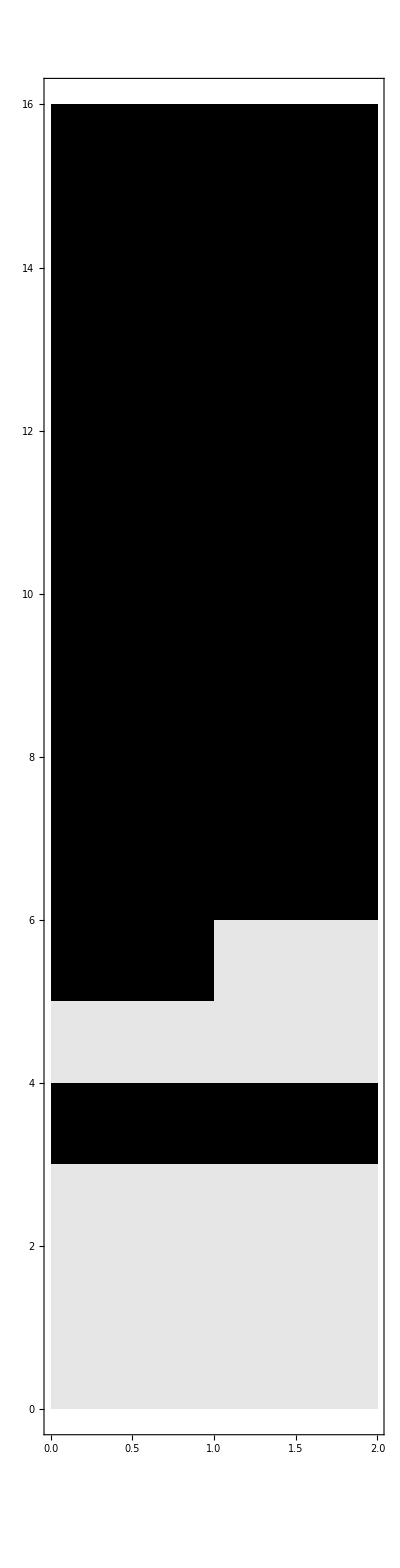
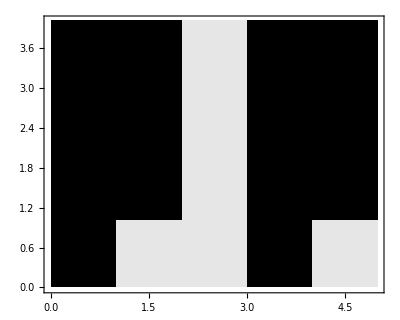
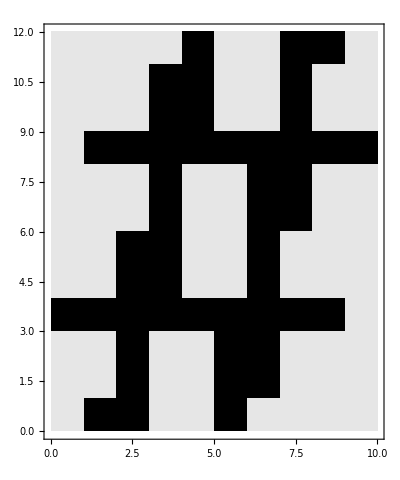
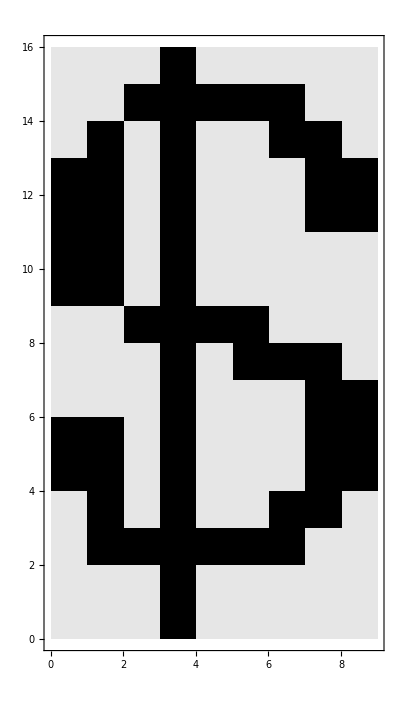
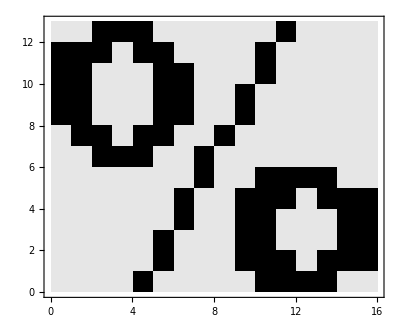
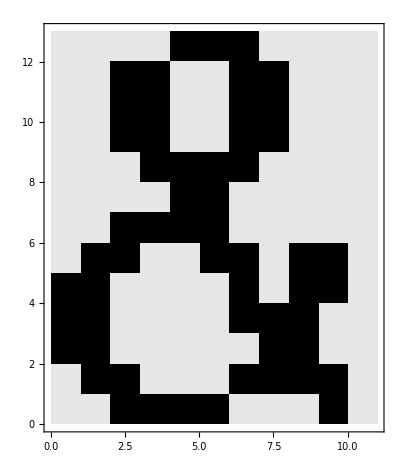
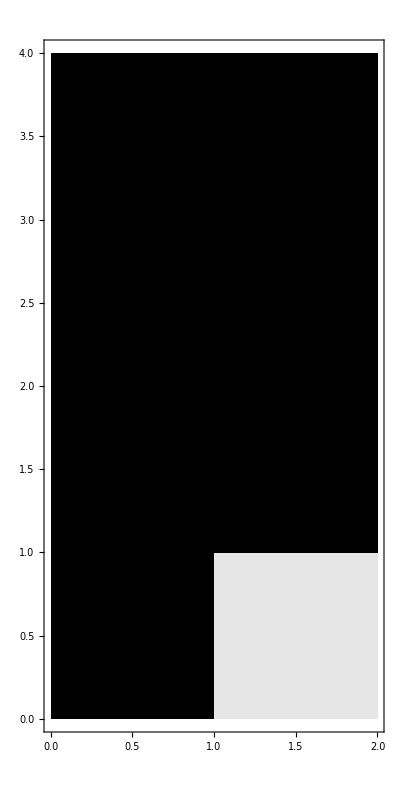
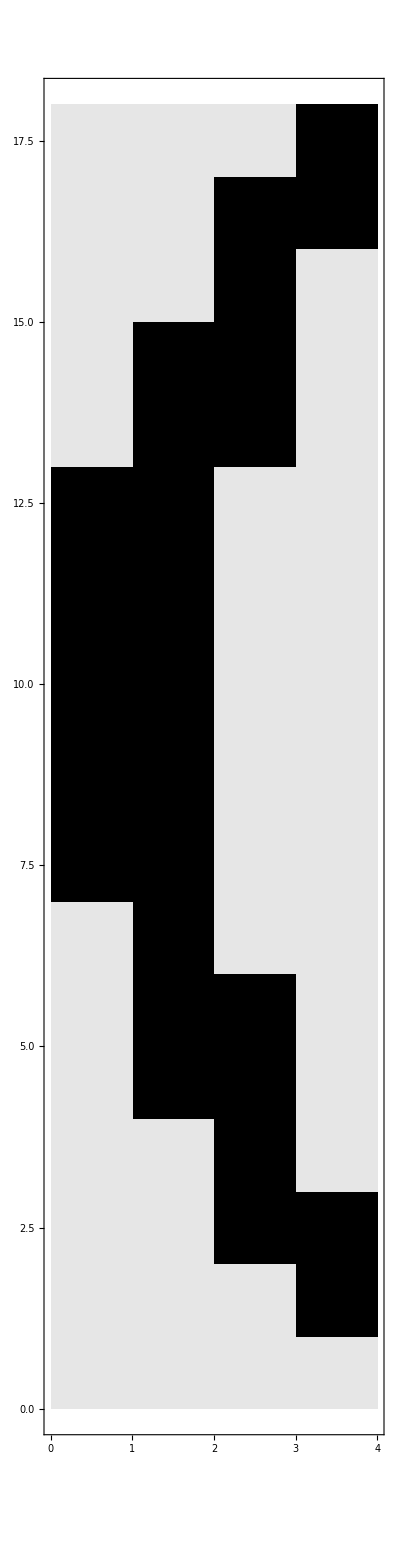
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[Raster[Reverse[.9(1-#)]],Frame->True,AspectRatio->Divide@@Dimensions[#]]&/@Rest[bitmaps]
```